# 概率统计

## 抛硬币

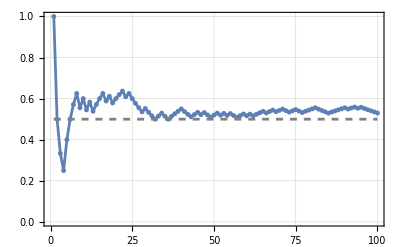

```mathematica
coins=RandomVariate[BernoulliDistribution[1/2],100];
Show[ListLinePlot[Table[Accumulate[coins][[i]]/i,{i,1,100}],PlotMarkers->{Automatic, 5},PlotTheme->"Detailed",PlotRange->All],Plot[1/2,{i,1,100},PlotStyle->{Gray,Dashed}]]
```

## 随机漫步

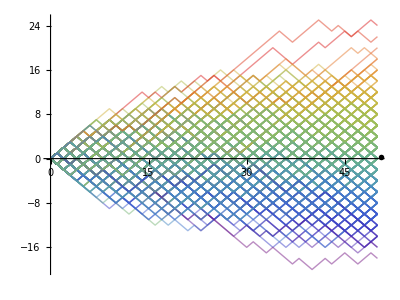

```mathematica
SeedRandom[1234];
data=RandomFunction[RandomWalkProcess[.5],{50},500]; (*正单位步长概率0.5，时间步50，路径数500*)
sd=data["SliceData",50]; (*在50处切片，可视化分布*)
cf=ColorData["Rainbow"];
sliced=BarChart[Last[#],Axes->False,BarOrigin->Left,AspectRatio->4,ChartStyle->(cf/@Rescale[MovingAverage[First[#],2],{Min[sd],Max[sd]},{0,1}]),ImageSize->60]&[HistogramList[sd,{Range[Min[sd],Max[sd],(Max[sd]-Min[sd])/15]}]];
ListLinePlot[data,ImageSize->400,PlotRange->All,AspectRatio->3/4,Epilog->Inset[sliced,{50.5,Mean[sd]},{0,8}],PlotStyle->(cf/@Rescale[sd]),BaseStyle->Directive[Thin,Opacity[0.5]],PlotRangePadding->{{0,20},{.5,7}}]
```